This is a notebook acompanying the file rec_2D_line.tex

```mathematica
SetDirectory["~/PET/pubs"]
```

/home/pbialas/PET/pubs

```mathematica
toProjectionSpaceTan[{y_,z_,t_},R_]:={z+ (R-y)t, z- (R+y) t,-2 y Sqrt[t^2+1]}
toProjectionSpaceTheta[{y_,z_,θ_},R_]:=toProjectionSpaceTan[{y,z,Tan[θ]},R]
```

```mathematica
LabeledArrow[{begin_,end_},text_]:={Arrowheads[{-.025,.025}],Arrow[{begin,end}],Text[text,1/2(begin+end),Background->White]}
```

```mathematica
drawDetector[{R_,L_}]:=Module[{},
{Line[{{-L/2,R},{L/2,R}}],Line[{{-L/2,-R},{L/2,-R}}]}
]
```

```mathematica
draw2DAxes[c_,{a1_,l1_,t1_,s1_ : 0.1 },{a2_,l2_,t2_, s2_ : 0.1}]:=Module[{},
{Thickness[0.001], Dashing[0.01], Arrow[{c-s1  l1 a1,c+a1 l1}], Arrow[{c-s2  l2 a2,c+a2 l2}]}
]
```

```mathematica
drawEvent[{y_,z_,θ_},R_]:=Module[{zu,zd,dl,m},
{zu,zd,dl}= toProjectionSpaceTheta[{y,z,θ},R];
{Line[{{zu,R},{zd,-R}}],{Red,PointSize[0.025],Point[{z,y}]}}
]
```

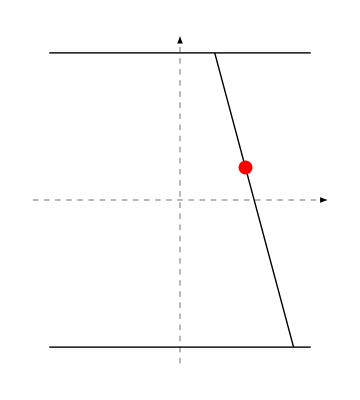

```mathematica
detector={drawDetector[{450,800}], draw2DAxes[{0,0},{{1,0},450,"z",1},{{0,1},500,"y",1}],drawEvent[{100,200,-15 Degree},450]}//Graphics
```

```mathematica
Export["detector.eps",detector,"EPS"]
```

detector.eps

```mathematica
resolution={30,90,10}
```

{30,90,10}

```mathematica
fromProjectionSpaceTan[{zu_,zd_,dl_},R_]:=Module[{t,y,z},
t=(zu-zd)/(2R);
y=-1/2 dl/Sqrt[1+t^2];
z = 1/2 (zu+zd+2 y t);
{y,z,t}
]
```

```mathematica
toProjectionSpaceTan[fromProjectionSpaceTan[{-200,300,100},450],450]//Simplify
```

{-200,300,100}

```mathematica
aVec[{y_,z_,θ_},R_]:={y-R, y+R, 2 y Sin[θ]}
```

```mathematica
bVec[{y_,z_,θ_},{dy_,dz_},R_]:={-dz +dy Tan[θ],-dz +dy Tan[θ],2 dy/Cos[θ]}
```

```mathematica
correlationMatrix[{sz_,sl_,η_}]={{sz^2,0,η},{0,sz^2,η},{η,η,sl^2}}
```

{{sz^2,0,η},{0,sz^2,η},{η,η,sl^2}}

```mathematica
iC[{sz_,sl_,η_}]:=Inverse[correlationMatrix[{sz,sl,η}]]
```

```mathematica
dtmin[{sz_,sl_,η_},{ty_,tz_,tθ_},{dy_,dz_},R_]:=Module[{b,a,ic},
ic=iC[{sz,sl,η}];
b=bVec[{ty,tz,tθ},{dy,dz},R];
a=aVec[{ty,tz,tθ},R];
b.ic.a/a.ic.a
]
```

```mathematica
dtmin[{30,100,10},{200,100,0 Degree},{50,150},450] //Expand //N
```

0.123631

```mathematica
gaussian[{sz_,sl_,η_},{ty_,tz_,tθ_},{dy_,dz_},R_]:=Module[{b,a,ic},
ic=iC[{sz,sl,η}];
b=bVec[{ty,tz,tθ},{dy,dz},R];
a=aVec[{ty,tz,tθ},R];
1/2 (b.ic.b - (b.ic.a)^2/a.ic.a)
]
```

```mathematica
gaussian[{30,100,10},{200,100,0 Degree},{dy,dz},450] //Expand //N
```

0.000200004 dy^2-3.71141×10^-6 dy dz+0.000927852 dz^2

```mathematica
approximateP[s_,meas_,{y_,z_},R_]:=Module[{ic,a,b,diff,tmin},
ic=iC[s];
a=aVec[meas,R];
diff={y-meas[[1]],z-meas[[2]]};
b=bVec[meas,diff,R];
tmin=meas[[3]]+dtmin[s,meas,diff,R];
Sqrt[Det[ic]/a.ic.a]/(2Pi^2) 1/(1+tmin^2) Exp[-gaussian[s,meas,diff,R]]
]
```

```mathematica
ap=approximateP[resolution,{0,0,30 Degree},{0,50.},450]
```

1.43865×10^-9

```mathematica
errorFunction[meas_,{y_,z_},s_,R_,t_]:= Module[{f,err,true},
true=toProjectionSpaceTan[{y,z,t},R];
err= meas-true;
f=1/2 err.iC[s].err
]
```

```mathematica
P[s_,meas_,{y_,z_,θ_},R_]:= Module[{f,ic},
ic=iC[s];
f=errorFunction[toProjectionSpaceTheta[meas,R],{y,z},s,R,Tan[θ]];
Sqrt[Det[ic]]/Sqrt[2 Pi]^3 Exp[-f]
]
```

```mathematica
P[resolution,{0,0,0},{0,0,θ},450]
```

(ⅇ^(-225 Tan[θ]^2))/(1200 √36449 π^(3/2))

```mathematica
P[s_,meas_,{y_,z_},R_]:= Module[{f,ic},
NIntegrate[P[s,meas,{y,z,θ},R],{θ,-Pi/2,Pi/2}]/Pi
]
```

```mathematica
exact=P[resolution,{0,0,30 Degree},{0,50},450]
```

1.43829×10^-9

```mathematica
ap/exact
```

1.00025

```mathematica
NIntegrate[P[resolution,fromProjectionSpaceTan[{zu,zd,dl},450],{0,0,30Degree},450],{zu,-500,500},{zd,-500,500},{dl, -750,750}]
```

1.

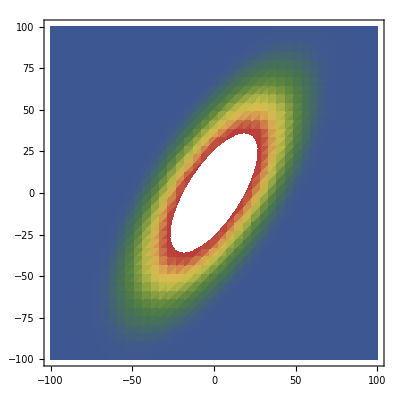

```mathematica
DensityPlot[P[resolution,{0,0,30Degree},{y,z},450],{z,-100,100},{y,-100,100},PlotPoints->40,ColorFunction->ColorData["DarkRainbow"]]
```

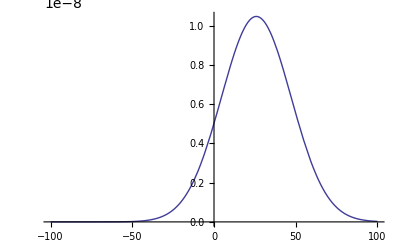

```mathematica
Plot[P[resolution,{0,0,30Degree},{50,z},450],{z,-100,100}]
```

```mathematica
compare[s_,meas_,{y_,z_},R_]:=Module[{e,a},
e=P[s,meas,{y,z},R];
a=approximateP[s,meas,{y,z},R];
{e,a,a-e,(a-e)/e}//N]
```

```mathematica
compare[resolution,{0,0,25 Degree},{0,0},450]
```

{2.42051×10^-8,2.47684×10^-8,5.63237×10^-10,0.0232693}

```mathematica
compare[resolution,{300,0,35 Degree},{320,10},450]
```

{1.38458×10^-8,1.51503×10^-8,1.30441×10^-9,0.0942093}

```mathematica
-2 ty Sqrt[1+tt^2]+2 (ty+ϵ dy)Sqrt[1+(tt+ϵ dt)^2]
```

-2 √(1+tt^2) ty+2 (ty+dy ϵ) √(1+(tt+dt ϵ)^2)

```mathematica
%+O[ϵ]^3
```

(2 (dy+dy tt^2+dt tt ty) ϵ)/(√(1+tt^2))+((2 dt dy tt+2 dt dy tt^3+dt^2 ty) ϵ^2)/((1+tt^2)^(3/2))+O[ϵ]^3

```mathematica
%//Simplify
```

(-2 √(1-tt^2) ty+2 √(1+tt^2) (ty+ϵdy))+(2 dt tt (ty+ϵdy) ϵ)/(√(1+tt^2))+(dt^2 (ty+ϵdy) ϵ^2)/((1+tt^2)^(3/2))+O[ϵ]^3

```mathematica
FindMaximum[P[resolution,{300,0,25 Degree},{300,0,t},450.],{t,25 Degree}]
```

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

{7.83883×10^-7,{t→0.436332}}

```mathematica
25 Degree  //N
```

0.436332

```mathematica
ArcTan[dtmin[resolution,{300,0,25 Degree},{0,0},450.]]+25 Degree
```

0.436332

```mathematica
dtmin[resolution,{300,0,25 Degree},{0,0},450.]
```

0.

```mathematica
P[resolution,{300,0,25 Degree},{300,0,t},450.]
```

1/(1200 √36449 π^(3/2))ⅇ^(1/2 (-(65.4498-150. Tan[t]) ((72899 (65.4498-150. Tan[t]))/65608200+(-327.249+750. Tan[t])/65608200+(600 √(1+625 °^2)-600 √(1+Tan[t]^2))/728980)-(-327.249+750. Tan[t]) ((65.4498-150. Tan[t])/65608200+(72899 (-327.249+750. Tan[t]))/65608200+(600 √(1+625 °^2)-600 √(1+Tan[t]^2))/728980)-(-600 √(1+625 °^2)+600 √(1+Tan[t]^2)) ((327.249-750. Tan[t])/728980+(-65.4498+150. Tan[t])/728980+(9 (-600 √(1+625 °^2)+600 √(1+Tan[t]^2)))/72898)))

```mathematica
1/(1200 √36449 π^(3/2))
```

```mathematica
1./(1200 √36449 π^(3/2))
```

7.83883×10^-7

```mathematica
P[resolution,{300,0,25 Degree},{300,0,25 Degree},450.]
```

5.83498×10^-7

```mathematica
errorFunction[toProjectionSpaceTheta[{300,0,25 Degree
```